```mathematica
{#,5#^(2/5),10 #^(2/5)}&/@{10,100,300,900,1500,3000}//N//Round
{#[[1]],X->{-#[[2]],#[[2]],200},Y->{-#[[3]],#[[3]],200}}&/@%//ToString
StringDelete[StringReplace[%,"}, {"->"
"],{" ","{{","}}"}]
```

{{10,13,25},{100,32,63},{300,49,98},{900,76,152},{1500,93,186},{3000,123,246}}

{{10, X -> {-13, 13, 200}, Y -> {-25, 25, 200}}, {100, X -> {-32, 32, 200}, Y -> {-63, 63, 200}}, {300, X -> {-49, 49, 200}, Y -> {-98, 98, 200}}, {900, X -> {-76, 76, 200}, Y -> {-152, 152, 200}}, {1500, X -> {-93, 93, 200}, Y -> {-186, 186, 200}}, {3000, X -> {-123, 123, 200}, Y -> {-246, 246, 200}}}

10,X->{-13,13,200},Y->{-25,25,200}
100,X->{-32,32,200},Y->{-63,63,200}
300,X->{-49,49,200},Y->{-98,98,200}
900,X->{-76,76,200},Y->{-152,152,200}
1500,X->{-93,93,200},Y->{-186,186,200}
3000,X->{-123,123,200},Y->{-246,246,200}

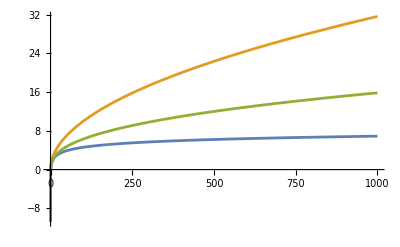

```mathematica
Plot[{Log[x],x^(1/2),x^(2/5)},{x,0,1000}]
```